# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Chapter 15 - Kinetics

## 15.1 DETERMINISTIC KINETICS

### 15.1.1 First-order reactions

```mathematica
k1=0.1; (*define rate constant*)
soln0=DSolve[{a'[t]==-k1*a[t],a[0]==1},a,t]
```

{{a→Function[{t},1. ⅇ^(-0.1 t)]}}

```mathematica
Evaluate[ a[10]/.soln0 ] (*analytical solution at t=10*)
```

{0.367879}

Erratum (first printing): p. 375 — Missing “{“ in last argument of NDSolve[]

```mathematica
soln1=NDSolve[ {a'[t]==-k1*a[t],a[0]==1},a,{t,0,10}][[1]]
```

{a→InterpolatingFunction[{{0., 10.}}, <>]}

```mathematica
Evaluate[a[10]/.soln1] (*numerical solution at t=10*)
```

0.367879

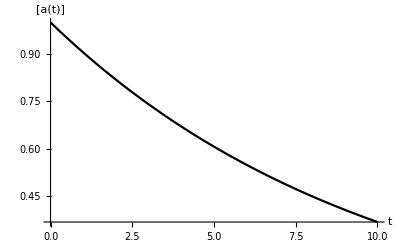

```mathematica
Plot[ Evaluate[a[t]/.soln1],{t,0,10},
PlotStyle->{Black},AxesLabel->{"t","[a(t)]"}]
```

### 15.1.2 Reversible first-order reactions

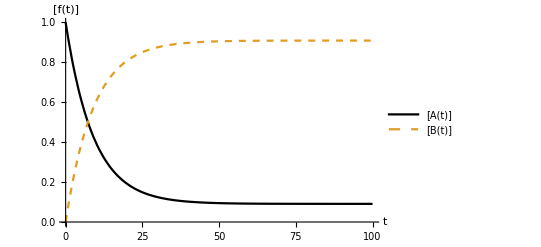

```mathematica
k1=0.1;(*define rate constants*)
k2=0.01;
soln2=NDSolve[
{a'[t]==-k1*a[t]+k2*b[t],b'[t]==+k1*a[t]-k2*b[t],a[0]==1,b[0]==0},{a,b},{t,0,100}][[1]];

Plot[ {Evaluate[a[t]/.soln2],Evaluate[b[t]/.soln2]},{t,0,100},PlotLegends->{"[A(t)]","[B(t)]"},
PlotStyle->{Black,Dashed},AxesLabel->{"t","[f(t)]"}]
```

### 15.1.3 Parallel first-order reactions

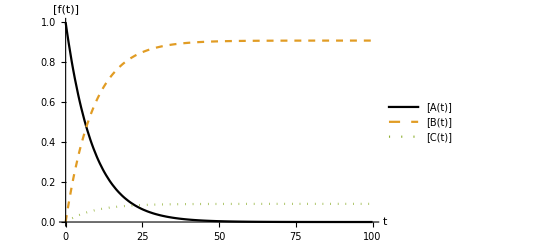

```mathematica
k1=0.1;(*define rate constants*)
k2=0.01;
soln3=NDSolve[
{a'[t]==-k1*a[t]-k2*a[t],
b'[t]==+k1*a[t],
c'[t]==+k2*a[t],
a[0]==1,b[0]==0,c[0]==0},
{a,b,c},{t,0,100}][[1]];

Plot[ {Evaluate[a[t]/.soln3],Evaluate[b[t]/.soln3],Evaluate[c[t]/.soln3]},{t,0,100},PlotLegends->{"[A(t)]","[B(t)]","[C(t)]"},PlotStyle->{Black,Dashed,Dotted},AxesLabel->{"t","[f(t)]"}]
```

### 15.1.4 Oscillatory reactions: The Lotka-Volterra reaction

```mathematica
k1=0.3; k2=0.6; k3=0.4; s=1.0; (*define rate constants*)

soln4=NDSolve[
{x'[t]==+k1*s*x[t]-k2*x[t]*y[t],
y'[t]==+k2*x[t]*y[t]-k3*y[t],
p'[t]==+k3*y[t],
x[0]==2.0,
y[0]==0.1,
p[0]==0 },
{x,y,p},{t,0,1000}][[1]];
```

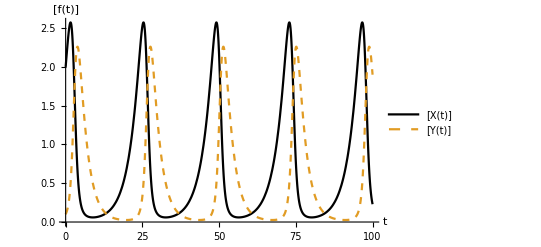

```mathematica
Plot[ {Evaluate[x[t]/.soln4],Evaluate[y[t]/.soln4]},{t,0,100},PlotLegends->{"[X(t)]","[Y(t)]"},
PlotStyle->{Black,Dashed},AxesLabel->{"t","[f(t)]"}]
```

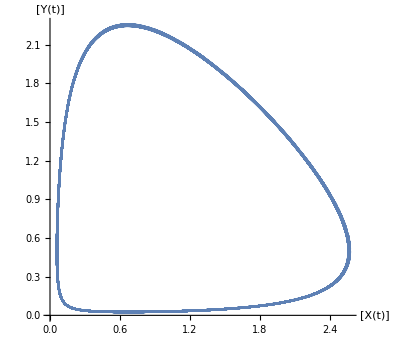

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.soln4],{t,0,1000},
AxesLabel->{"[X(t)]","[Y(t)]"} ]
```

```mathematica
k1=0.3; k2=0.6; k3=0.4; s=1.0; (*define rate constants*)
soln5=NDSolve[
{x'[t]==+k1*s*x[t]-k2*x[t]*y[t]+10^-4*RandomReal[{-1,+1}],y'[t]==+k2*x[t]*y[t]-k3*y[t],
p'[t]==+k3*y[t],
x[0]==2.0,y[0]==0.1,p[0]==0},
{x,y,p},{t,0,1000}][[1]];
```

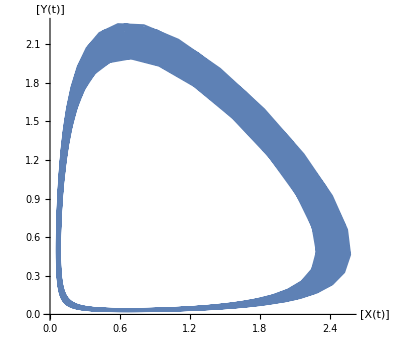

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.soln5],{t,0,1000},
AxesLabel->{"[X(t)]","[Y(t)]"}]
```

## 15.2 STOCHASTIC KINETICS

### 15.2.1 Kinetic Monte Carlo algorithm

```mathematica
drawTime[wtotal_]:=(-1/wtotal)*Log[RandomReal[]];
```

### 15.2.2 First-order reactions

```mathematica
k1=0.1;(*define rate constants*)
nA=100;(*number of starting particles*)
currentTime=0;(*initial time*)
trajectory={{currentTime,nA}};(*state of the system with time*)

While[(nA>0),(*run simulation while reactant A remains*)
rate1=k1*nA; (*compute the reaction rates; here only one is possible*)
rateTotal=rate1;

nA-=1; (*pick a reaction to occur;here only one is possible*)
currentTime+=drawTime[rateTotal];(*update time*)

AppendTo[trajectory,{currentTime,nA}];(*update trajectory*)
];
```

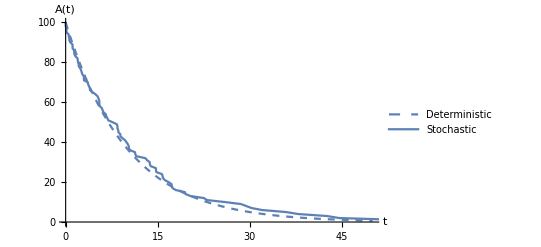

```mathematica
Show[
Plot[100*Exp[-k1*t],{t,0,50},
PlotLegends->{"Deterministic"},
PlotStyle->{Dashed},AxesLabel->{"t","A(t)"}],
ListPlot[trajectory,
PlotLegends->{"Stochastic"},Joined->True] ]
```

### 15.2.3 Reversible first-order reactions

```mathematica
k1=0.1;k2=0.01;(*define rate constants*)
nA=100;nB=0;currentTime=0; (*define initial conditions*)
trajectoryA={{currentTime,nA}}; trajectoryB={{currentTime,nB}};
While[(currentTime<2000),
rate1=k1*nA;(*compute rates of possible reactions*)
rate2=k2*nB;
rateTotal=rate1+rate2;
If[(RandomReal[{0,rateTotal}]≤rate1),(*select reaction*)
nA--;nB++;,(*reaction 1: forward reaction*)
nA++;nB--;    (*reaction 2:reverse reaction*)
];
currentTime+=drawTime[rateTotal];(*update time*)
AppendTo[trajectoryA,{currentTime,nA}];AppendTo[trajectoryB,{currentTime,nB}];
];
```

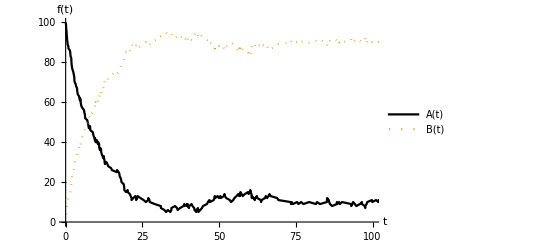

```mathematica
ListPlot[ {trajectoryA,trajectoryB},
PlotRange->{{0,100},{0,100}},
PlotLegends->{"A(t)","B(t)"},
Joined->True,PlotStyle->{Black,Dotted},
PlotMarkers->None,AxesLabel->{"t","f(t)"}]
```

### 15.2.4 Parallel first-order reactions

```mathematica
stochasticParallelFirstOrder[k1_,k2_,startA_,startB_,startC_,maxTime_]:=
Module[
{currentTime=0,nA=startA,nB=startB,nC=startC,
trajA={{0,startA}},trajB={{0,startB}},trajC={{0,startC}},rateList={0,0},random,whichRxn},

While[(currentTime≤maxTime)&&(nA>0),
rateList[[1]]=k1*nA;(*construct the list of rates*)
rateList[[2]]=rateList[[1]]+k2*nA;

random=RandomReal[{0,Last[rateList]}];
whichRxn=1;
Do[ (*determine which reaction happened...*)If[rateList[[i-1]]<random≤rateList[[i]],whichRxn=i; ];
,{i,2,Length[rateList]}];

If[whichRxn==1,nA--;nB++;];(*...then do it!*) 
If[whichRxn==2,nA--;nC++;];

currentTime+=drawTime[Last[rateList]];(*update time*)
AppendTo[trajA,{currentTime,nA}];(*update trajectories*)
AppendTo[trajB,{currentTime,nB}];AppendTo[trajC,{currentTime,nC}];
];
{trajA,trajB,trajC} (*return the trajectory lists*)
];
```

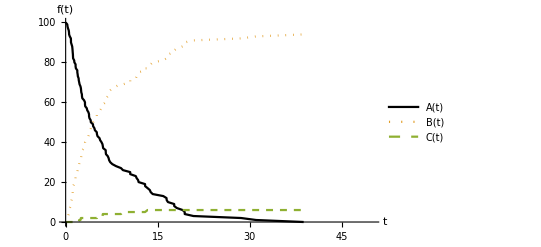

```mathematica
k1=0.1;k2=0.01;(*define rate constants*)
ListPlot[
stochasticParallelFirstOrder[k1,k2,100,0,0,100],
PlotRange->{{0,50},{0,100}},
PlotLegends->{"A(t)","B(t)","C(t)"},
Joined->True,PlotStyle->{Black,Dotted,Dashed},
AxesLabel->{"t","f(t)"}]
```

Note:  I’ve modified the colors as described in the text

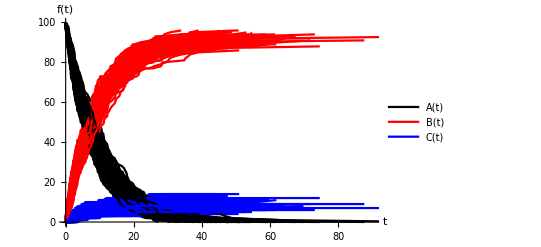

```mathematica
k1=0.1; k2=0.01;
multipleTrajectories={}; colorList={};
Do[ (*repeat 100 trials*){trajA,trajB,trajC}=stochasticParallelFirstOrder[k1,k2,100,0,0,100];
AppendTo[multipleTrajectories,trajA];
AppendTo[multipleTrajectories,trajB];
AppendTo[multipleTrajectories,trajC];
AppendTo[colorList,Black];
AppendTo[colorList,Red]; (*suggested modification described in text*)
AppendTo[colorList,Blue];(*suggested modification described in text*)
,{100}];

ListPlot[ multipleTrajectories,
PlotRange->{{0,90},{0,100}},
PlotLegends->{"A(t)","B(t)","C(t)"},
Joined->True,PlotStyle->colorList,PlotMarkers->None,
AxesLabel->{"t","f(t)"}]
```

```mathematica
finalTimes={};
Do[ (*loop over independent trajectories*){trajA,trajB,trajC}=stochasticParallelFirstOrder[k1,k2,100,0,0,200];
AppendTo[finalTimes,trajA[[-1,1]]];
,{1000}]
```

```mathematica
{Mean[finalTimes],Median[finalTimes]}
```

{46.0894,44.4377}

```mathematica
{Min[finalTimes],Max[finalTimes]}
```

{23.2356,100.765}

```mathematica
{Quantile[finalTimes,0.1],Quantile[finalTimes,0.9]}
```

{33.7647,60.5938}

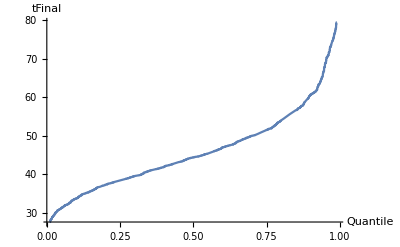

```mathematica
Plot[ Quantile[finalTimes,x],{x,0.01,0.99},
AxesLabel->{"Quantile","tFinal"} ]
```

```mathematica
finalCBratios={};
Do[
{trajA,trajB,trajC}=stochasticParallelFirstOrder[k1,k2,100,0,0,200];
AppendTo[finalCBratios,(trajC[[-1,2]]/trajB[[-1,2]])];
,{1000}];
```

```mathematica
{Mean[finalCBratios],Median[finalCBratios]}//N
```

{0.102222,0.0989011}

```mathematica
Evaluate[(c[100]/b[100])/.soln3]
```

0.1

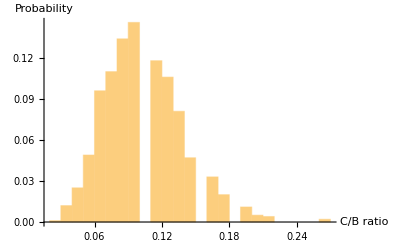

```mathematica
Histogram[ finalCBratios,Automatic,"Probability",AxesLabel->{"C/B ratio","Probability"} ]
```

### 15.2.5 Lotka-Volterra reaction

```mathematica
stochasticLotkaVolterra[k1_,k2_,k3_,startS_,startX_,startY_,maxTime_]:=
Module[
{currentTime=0,nX=startX,nY=startY,
trajX={{0,startX}},trajY={{0,startY}},
rateList={0,0,0},random,whichRxn},

While[(currentTime≤maxTime)&&((nX>0)||(nY>0)),
rateList[[1]]=k1*nX*startS;(*construct the list of rates*)
rateList[[2]]=rateList[[1]]+k2*nX*nY;rateList[[3]]=rateList[[2]]+k3*nY;

random=RandomReal[{0,Last[rateList]}];
whichRxn=1;
Do[ (*determine which reaction happened...*)If[rateList[[i-1]]<random≤rateList[[i]],whichRxn=i;];
,{i,2,Length[rateList]}];

If[whichRxn==1,nX++;];(*...then do it!*)
If[whichRxn==2,nX--;nY++;];
If[whichRxn==3,nY--;];

currentTime+=drawTime[Last[rateList]];(*update time*)
AppendTo[trajX,{currentTime,nX}];(*update trajectories*)
AppendTo[trajY,{currentTime,nY}];
];
{trajX,trajY} (*return trajectory lists*)
];
```

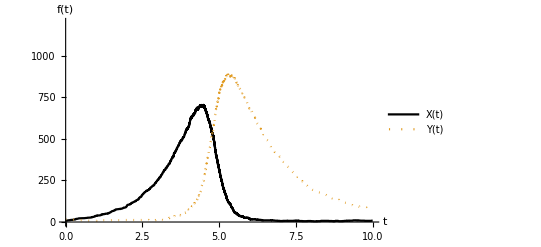

```mathematica
k1=1;k2=0.005;k3=0.6;(*define rate constants*)
ListPlot[ stochasticLotkaVolterra[k1,k2,k3,1,8,16,10],PlotRange->{{0,10},{0,1200}},
PlotLegends->{"X(t)","Y(t)"},
Joined->True,PlotStyle->{Black,Dotted},
PlotMarkers->None,AxesLabel->{"t","f(t)"} ]
```

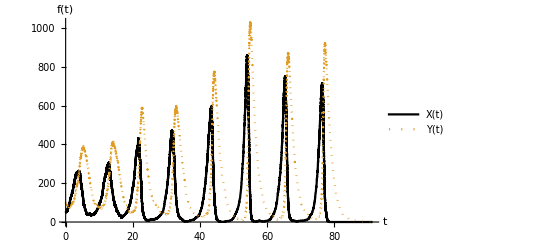

```mathematica
{trajX,trajY}=stochasticLotkaVolterra[k1,k2,k3,1,50,100,100000];

ListPlot[ {trajX,trajY},
PlotLegends->{"X(t)","Y(t)"},
Joined->True,PlotStyle->{Black,Dotted},
PlotMarkers->None,AxesLabel->{"t","f(t)"}]
```

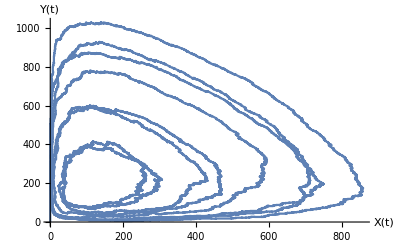

```mathematica
xyParamList={};
Do[
AppendTo[xyParamList,{trajX[[i,2]],trajY[[i,2]]}]
,{i,Length[trajX]}];
ListPlot[ xyParamList,
Joined->True,PlotMarkers->None,AxesLabel->{"X(t)","Y(t)"} ]
```